```mathematica
f[x_]:=1/(1+x^2);
```

```mathematica
a=-1;b=1;n=5;
```

```mathematica
(*gridX=Table[a+i*(b-a)/n,{i,0,n}];*)(*Равномерная сетка*)
```

```mathematica
gridX=Table[(a+b)/2+(b-a)/2 Cos[((2*i+1)*π)/(2*(n+1))],{i,0,n}];(*Чебышевская сетка*)
```

```mathematica
gridY=f[gridX];
```

```mathematica
A=gridY[[1;;-2]];H=Table[gridX[[i]]-gridX[[i-1]],{i,2,n+1}];G=Table[(gridY[[i]]-gridY[[i-1]])/H[[i-1]],{i,2,n+1}];
```

```mathematica
Matrix=Table[{H[[i-1]],2*(H[[i-1]]+H[[i]]),H[[i]]},{i,2,n}];
```

```mathematica
Matrix[[1]][[1]]=0;Matrix[[-1]][[-1]]=0;
```

```mathematica
right=Table[3*(G[[i]]-G[[i-1]]),{i,2,n}];
```

```mathematica
α={(-Matrix[[1]][[3]])/(Matrix[[1]][[2]])};β={right[[1]]/(Matrix[[1]][[2]])};
```

```mathematica
For[i=2,i<n,i++,
α=Insert[α,(-Matrix[[i-1]][[3]])/(Matrix[[i-1]][[2]]+Matrix[[i-1]][[1]]*α[[i-1]]),-1];
β=Insert[β,(right[[i-1]]-Matrix[[i-1]][[1]]*β[[i-1]])/(Matrix[[i-1]][[2]]+Matrix[[i-1]][[1]]*α[[i-1]]),-1];
]
```

```mathematica
Systemsol=Table[0,{i,1,n-1}];
```

```mathematica
Systemsol[[n-1]]=(right[[n-1]]-Matrix[[n-1]][[1]]*β[[n-1]])/(Matrix[[n-1]][[2]]+Matrix[[n-1]][[1]]*α[[n-1]]);
```

```mathematica
For[k=n-2,k>=1,k--,
Systemsol[[k]]=Systemsol[[k+1]]*α[[k+1]]+β[[k+1]];
]
```

```mathematica
Cm=Systemsol;
```

```mathematica
Cm=Insert[Cm,0,1];
```

```mathematica
B=Table[G[[i]]-((Cm[[i+1]]+2Cm[[i]])*H[[i]])/3,{i,1,n-1}];
```

```mathematica
B=Insert[B,G[[n]]-(2Cm[[n]]*H[[n]])/3,-1];
```

```mathematica
Dm=Table[(Cm[[i+1]]-Cm[[i]])/(3H[[i]]),{i,1,n-1}];
```

```mathematica
Dm=Insert[Dm,(-Cm[[n]])/(3H[[i]]),-1 ];
```

```mathematica
cubics=Table[A[[i]]+B[[i]](x-gridX[[i]])+Cm[[i]](x-gridX[[i]])^2+Dm[[i]](x-gridX[[i]])^3,{i,1,n}];
```

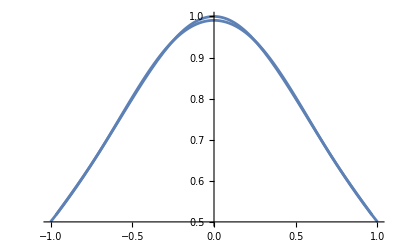

```mathematica
Show[Plot[f[x],{x,-1,1}],Table[Plot[cubics[[i]],{x,gridX[[i]],gridX[[i+1]]}],{i,1,n}]]
```